```mathematica
ClearAll[Evaluate[Context[]<>"*"]]
```

```mathematica
rawdata=Import["/home/luca/Documents/ReplyChallenges/STANDARD CODE CHALLENGE 2022 - PANDORA'S ADVENTURES/inputs/02-iot-island-of-terror.txt","Table"];
{staminaInit,staminaMax,turnsNum,demonsNum}=rawdata[[1]];
demons=rawdata[[2;;,1;;3]];
fragments=rawdata[[2;;,5;;]];
fragments=fragments[[;;(Position[fragments,Except[0|0.|Null],1][[-1,1]])]];
fragments=fragments/.{}->{0};
fragments=Map[Take[#,UpTo[turnsNum]]&,fragments];
demonsWithFragments=Flatten/@Flatten[{demons,Total[fragments,{2}]},{2}];
```

## Files 01,02,04

Ho trovato le distribuzioni con cui si generano la quantità di stamina ricoverata e anche il numero di turni per recuperare la stamina.

```mathematica
Round@RandomVariate[CensoredDistribution[{10,100},NormalDistribution[49,20]],100000];
KolmogorovSmirnovTest[%,demons[[All,2]],{"PValue","ShortTestConclusion"}]
```

{0.952004,Do not reject}

```mathematica
Round@RandomVariate[CensoredDistribution[{10,40},NormalDistribution[7.5,8.5]],100000];
KolmogorovSmirnovTest[%,demons[[All,3]],{"PValue","ShortTestConclusion"}]
```

{0.859547,Do not reject}

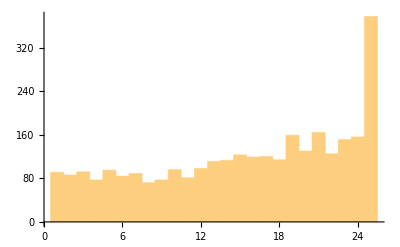

DataDistribution[…]

```mathematica
data=demons[[All,1]];
Histogram@data
FindDistribution[data]
```

```mathematica
ListPlot@Map[CoefficientList[Fit[#, {1,x},x],x]&,fragments]
```

ListPlot::lpn: {{{1., 3.93333}, {2., 0.257143}}, {}, {<<2>>}, <<499996>>, {{1., 1.}, {2., 0.8}}} is not a list of numbers or pairs of numbers.

ListPlot[{{3.93333,0.257143},{},{4.,3.},{},{},{},{},{},{10.,-3.},499982,{},{},{128.571,-4.80415×10^-15},{5.15789,0.0263158},{},{},{},{9.26667,-0.6},{1.,0.8}}]
 |  |  |  |

```mathematica
Position[yolo,n_ /; n>5]
```

{{193},{286},{421}}

```mathematica
fragments[[421]]
```

{3,9}

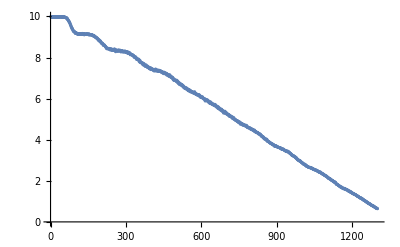

1165

8451597

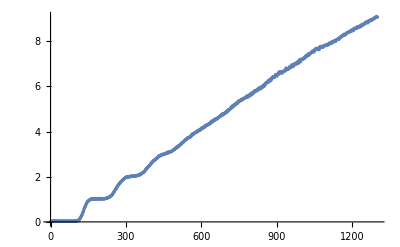

1178

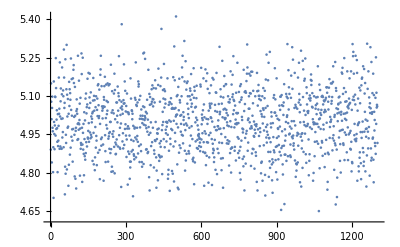

657

```mathematica
Select[fragments,((#[[1]]==10∧#[[-1]]==0))&];
ListPlot@Mean@%[[All,1;;Min[Length/@%]]]
Length@%%
Total@Flatten@%%%

Select[fragments,((#[[1]]==0∧#[[-1]]==10))&];
ListPlot@Mean@%[[All,1;;Min[Length/@%]]]
Length@%%

Select[fragments,¬((#[[1]]==10∧#[[-1]]==0)∨(#[[1]]==0∧#[[-1]]==10))&];
ListPlot@Mean@%[[All,1;;Min[Length/@%]]]
Length@%%
```

```mathematica
Tally@Map[Length[#]==turnsNum&,fragments]
```

{{False,2013},{True,987}}

```mathematica
Flatten@Position[fragments,_List?(Length[#]==turnsNum&)]
```

{4,5,6,7,9,13,15,21,31,32,33,34,38,39,40,44,47,53,56,61,65,69,76,78,79,81,87,88,90,93,95,102,104,106,110,117,118,119,121,131,133,136,137,139,142,144,146,148,149,154,160,162,165,167,168,176,177,181,183,194,195,197,204,206,208,209,211,212,214,216,219,226,227,233,234,235,238,241,243,247,248,253,257,259,261,265,267,268,269,271,272,274,282,286,289,296,297,298,299,300,306,322,324,327,329,331,336,339,340,341,349,351,356,358,362,365,367,370,371,373,374,377,381,385,387,390,396,400,404,408,409,410,411,413,415,418,422,425,426,427,430,431,433,434,438,442,444,447,448,450,451,456,461,463,464,465,466,469,476,478,479,480,483,485,487,489,491,492,495,500,502,509,514,521,525,530,532,534,535,536,544,545,547,548,550,551,557,560,567,569,570,576,577,578,579,581,583,584,585,589,591,593,594,599,600,605,606,609,614,615,617,620,622,626,630,631,634,635,637,639,640,641,642,646,649,655,657,659,660,665,666,672,675,677,678,679,681,683,688,695,702,707,708,715,716,722,727,730,733,739,743,746,747,752,753,755,760,761,771,772,779,784,786,787,789,791,794,795,797,798,799,802,806,809,813,815,824,825,826,829,830,833,835,836,838,839,842,843,859,860,861,865,866,873,874,880,881,888,890,897,899,906,907,909,913,914,915,916,918,920,921,922,923,924,928,932,933,934,935,936,942,943,946,952,958,961,964,965,966,971,974,978,981,985,986,995,1001,1002,1008,1013,1015,1021,1030,1034,1035,1046,1047,1048,1056,1057,1059,1060,1062,1067,1068,1072,1074,1082,1087,1088,1089,1090,1092,1093,1094,1096,1099,1101,1103,1109,1113,1115,1118,1120,1124,1126,1132,1136,1137,1138,1147,1148,1149,1150,1152,1153,1154,1157,1160,1161,1163,1170,1171,1178,1185,1186,1188,1190,1195,1197,1200,1201,1204,1205,1206,1209,1210,1217,1218,1221,1222,1225,1226,1228,1232,1236,1238,1246,1247,1248,1255,1259,1264,1266,1267,1268,1270,1271,1273,1278,1279,1280,1281,1285,1287,1288,1289,1290,1293,1299,1303,1307,1310,1312,1314,1315,1322,1323,1324,1328,1329,1330,1331,1336,1338,1340,1346,1347,1350,1351,1356,1362,1370,1372,1379,1383,1384,1388,1390,1391,1399,1401,1402,1405,1406,1410,1412,1413,1416,1423,1433,1437,1438,1439,1443,1445,1452,1453,1459,1463,1464,1474,1475,1478,1479,1483,1486,1489,1493,1495,1505,1507,1513,1522,1526,1528,1529,1530,1535,1537,1540,1542,1546,1554,1556,1560,1561,1565,1566,1571,1576,1577,1579,1583,1587,1588,1590,1595,1596,1597,1598,1602,1617,1619,1625,1630,1631,1632,1633,1635,1647,1649,1651,1652,1663,1667,1671,1674,1679,1682,1685,1687,1688,1690,1691,1692,1693,1694,1695,1699,1701,1702,1703,1706,1709,1719,1721,1723,1726,1727,1728,1735,1738,1744,1748,1752,1753,1757,1762,1765,1766,1767,1772,1778,1780,1781,1784,1787,1789,1791,1793,1795,1803,1804,1811,1812,1814,1815,1818,1819,1821,1822,1827,1828,1830,1835,1838,1839,1844,1845,1847,1849,1851,1852,1858,1860,1862,1866,1868,1870,1874,1875,1876,1883,1886,1891,1892,1894,1897,1898,1905,1909,1910,1916,1917,1921,1927,1928,1932,1935,1936,1938,1940,1941,1950,1953,1957,1960,1966,1967,1968,1973,1975,1985,1987,1988,1989,1991,1993,1997,1998,2001,2006,2011,2013,2014,2017,2020,2024,2029,2030,2032,2033,2034,2038,2043,2044,2046,2049,2054,2055,2056,2058,2061,2064,2066,2067,2072,2075,2077,2078,2092,2105,2107,2108,2111,2112,2113,2115,2120,2122,2125,2137,2139,2144,2145,2150,2152,2155,2156,2158,2159,2161,2164,2165,2173,2176,2180,2183,2185,2186,2187,2192,2193,2194,2195,2198,2202,2207,2210,2217,2219,2223,2224,2227,2228,2229,2231,2234,2236,2241,2243,2245,2246,2248,2251,2252,2253,2254,2255,2256,2265,2273,2283,2286,2288,2289,2290,2298,2304,2307,2311,2316,2318,2320,2321,2324,2326,2327,2328,2329,2330,2331,2332,2336,2338,2344,2346,2347,2349,2357,2360,2362,2363,2364,2366,2367,2375,2379,2385,2386,2391,2392,2395,2396,2397,2399,2403,2408,2409,2411,2412,2417,2423,2426,2427,2429,2433,2435,2437,2439,2443,2449,2450,2452,2453,2454,2456,2459,2469,2470,2472,2474,2475,2476,2478,2484,2486,2487,2488,2489,2490,2491,2492,2493,2494,2496,2498,2502,2504,2507,2512,2514,2515,2518,2522,2524,2531,2536,2537,2540,2548,2552,2553,2555,2556,2559,2561,2564,2565,2567,2569,2575,2585,2586,2590,2595,2599,2600,2604,2606,2612,2613,2614,2621,2624,2626,2628,2631,2633,2634,2636,2638,2641,2642,2651,2652,2655,2660,2663,2665,2670,2671,2672,2674,2675,2676,2677,2683,2686,2688,2690,2699,2702,2705,2708,2710,2713,2724,2726,2728,2732,2734,2739,2744,2749,2750,2754,2756,2764,2766,2771,2776,2780,2791,2795,2796,2797,2799,2802,2806,2809,2812,2814,2830,2832,2834,2835,2838,2839,2848,2849,2856,2867,2868,2871,2873,2874,2881,2883,2886,2889,2891,2897,2900,2901,2906,2908,2911,2912,2914,2922,2924,2930,2934,2936,2937,2940,2944,2945,2947,2949,2952,2955,2958,2959,2960,2966,2967,2971,2975,2977,2982,2983,2985,2991,2997}

## File 03

```mathematica
Count[fragments,{0}]
N[%/demonsNum]
```

263062

0.526124

```mathematica
MinMax/@Transpose@demons
```

{{3,35},{1,150},{4,40}}

```mathematica
Show[ListPointPlot3D[Union@demons,AxesLabel->{"stamina consumed","turns","stamina recovered"},BoxRatios->Automatic],RegionPlot3D[Abs[x-z]<2,{x,3,35},{y,1,150},{z,4,40}]]
```

-Graphics3D-

```mathematica
goodDemonsIdx=Flatten@Position[demons,_List?(#[[3]]≥25&)];
badDemonsIdx=Flatten@Position[demons,_List?(#[[1]]≥25&)];
otherDemonsIdx=Complement[Range[demonsNum],goodDemonsIdx,badDemonsIdx];
Length@goodDemonsIdx
Length@badDemonsIdx
Length@otherDemonsIdx
```

211938

212224

75838

```mathematica
fastDemonsIdx=Flatten@Position[demonsWithFragments,_List?((#[[2]]==1)&)];
Length@fastDemonsIdx
Tally@demonsWithFragments[[fastDemonsIdx]]
(*SortBy[demonsWithFragments[[fastDemonsIdx]],Last][[-33;;]]
Total[%[[All,4]]]*)
```

9489

{{{7,1,4,520},50},{{3,1,8,0},4786},{{7,1,4,1320},43},{{7,1,4,1200},41},{{7,1,4,60},25},{{7,1,4,1580},37},{{7,1,4,0},234},{{7,1,4,1040},49},{{7,1,4,1120},44},{{7,1,4,1660},42},{{7,1,4,140},45},{{7,1,4,760},40},{{7,1,4,660},40},{{7,1,4,380},46},{{7,1,4,540},44},{{7,1,4,1140},44},{{7,1,4,1640},43},{{7,1,4,740},38},{{7,1,4,1300},34},{{7,1,4,20},34},{{7,1,4,1000},49},{{7,1,4,460},38},{{7,1,4,2460},4},{{7,1,4,600},37},{{7,1,4,1920},32},{{7,1,4,1100},43},{{7,1,4,900},56},{{7,1,4,1060},36},{{7,1,4,1600},38},{{7,1,4,800},45},{{7,1,4,1740},39},{{7,1,4,1520},45},{{7,1,4,720},40},{{7,1,4,320},36},{{7,1,4,220},42},{{7,1,4,640},64},{{7,1,4,280},39},{{7,1,4,1980},22},{{7,1,4,1720},48},{{7,1,4,100},45},{{7,1,4,480},54},{{7,1,4,1560},41},{{7,1,4,1940},28},{{7,1,4,1340},46},{{7,1,4,360},48},{{7,1,4,160},46},{{7,1,4,2020},20},{{7,1,4,300},61},{{7,1,4,980},39},{{7,1,4,1260},50},{{7,1,4,1440},67},{{7,1,4,240},39},{{7,1,4,1760},35},{{7,1,4,700},44},{{7,1,4,620},37},{{7,1,4,2040},25},{{7,1,4,340},45},{{7,1,4,1960},28},{{7,1,4,1620},40},{{7,1,4,580},38},{{7,1,4,1220},41},{{7,1,4,840},41},{{7,1,4,200},64},{{7,1,4,1480},52},{{7,1,4,680},48},{{7,1,4,2160},14},{{7,1,4,1380},48},{{7,1,4,1240},53},{{7,1,4,1460},41},{{7,1,4,1400},38},{{7,1,4,1860},24},{{7,1,4,1680},41},{{7,1,4,2140},12},{{7,1,4,2360},8},{{7,1,4,1820},34},{{7,1,4,1020},42},{{7,1,4,120},47},{{7,1,4,780},40},{{7,1,4,260},38},{{7,1,4,1840},35},{{7,1,4,920},41},{{7,1,4,1420},27},{{7,1,4,80},28},{{7,1,4,40},27},{{7,1,4,860},41},{{7,1,4,1160},45},{{7,1,4,1180},41},{{7,1,4,180},42},{{7,1,4,2080},28},{{7,1,4,560},47},{{7,1,4,1900},35},{{7,1,4,1540},38},{{7,1,4,1800},28},{{7,1,4,440},41},{{7,1,4,820},46},{{7,1,4,2000},31},{{7,1,4,940},37},{{7,1,4,2120},22},{{7,1,4,400},52},{{7,1,4,1700},45},{{7,1,4,880},59},{{7,1,4,960},37},{{7,1,4,1360},45},{{7,1,4,420},41},{{7,1,4,2100},20},{{7,1,4,1500},51},{{7,1,4,1880},32},{{7,1,4,1080},49},{{7,1,4,1280},51},{{7,1,4,2400},2},{{7,1,4,500},41},{{7,1,4,2280},9},{{7,1,4,2340},7},{{7,1,4,1780},39},{{7,1,4,2200},13},{{7,1,4,2180},18},{{7,1,4,2620},2},{{7,1,4,2220},8},{{7,1,4,2480},5},{{7,1,4,2320},3},{{7,1,4,2580},3},{{7,1,4,2060},21},{{7,1,4,2300},10},{{7,1,4,2440},4},{{7,1,4,2880},1},{{7,1,4,2700},2},{{7,1,4,2260},5},{{7,1,4,2420},3},{{7,1,4,2380},6},{{7,1,4,2240},6},{{7,1,4,2720},1},{{7,1,4,2680},1},{{7,1,4,2500},1},{{7,1,4,2540},1},{{7,1,4,2940},1}}

{{{7,1,4},4469}}

## Old Code

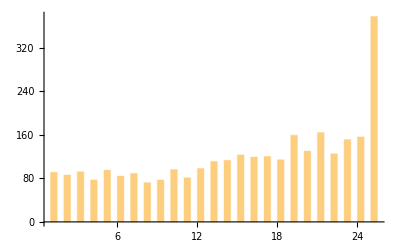

```mathematica
Histogram[demons[[All,1]],{0.5},PlotRange->All]
```

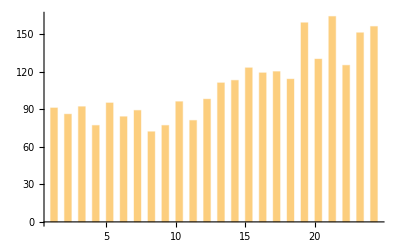

{72,164}

```mathematica
Histogram[Select[demons,#[[1]]<25&][[All,1]],{0.5},PlotRange->All]
MinMax[Tally[Select[demons,#[[1]]<25&][[All,1]]][[All,2]]]
```

```mathematica
DistributionFitTest[Select[demons,#[[1]]<25&][[All,1]],DiscreteUniformDistribution[{1,24}]]
```

1.53105×10^-22

```mathematica
DistributionFitTest[RandomInteger[{1,24},Length@Select[demons,#[[1]]<25&]],DiscreteUniformDistribution[{1,24}]]
DistributionFitTest[RandomInteger[{1,24},Length@Select[demons,#[[1]]<25&]],DiscreteUniformDistribution[{1,24}]]
DistributionFitTest[RandomInteger[{1,24},Length@Select[demons,#[[1]]<25&]],DiscreteUniformDistribution[{1,24}]]
DistributionFitTest[RandomInteger[{1,24},Length@Select[demons,#[[1]]<25&]],DiscreteUniformDistribution[{1,24}]]
DistributionFitTest[RandomInteger[{1,24},Length@Select[demons,#[[1]]<25&]],DiscreteUniformDistribution[{1,24}]]
DistributionFitTest[RandomInteger[{1,24},Length@Select[demons,#[[1]]<25&]],DiscreteUniformDistribution[{1,24}]]
```

0.225342

0.922907

0.916231

0.138139

0.828101

0.762577

```mathematica
(*𝒟[x_,f_,λ_,v_]:=If[x==v,λ+(1-λ)f[v],(1-λ)Evaluate[f[x]]];
Show[Histogram[demons[[All,1]],{0.5},"Probability"],DiscretePlot[𝒟[x,Function[s,PDF[DiscreteUniformDistribution[{1,25}],s]],1/10,25],{x,-1,30},PlotStyle->Thick],PlotRange->All]*)
```

Piecewise[{{0, x<10}, {1/2 Erfc[(-10+μ)/(√2 σ)], x==10}, {1/2 (Erf[(1-μ+Ceiling[x])/(√2 σ)]-Erf[(-μ+Floor[x])/(√2 σ)]), True}}]

{0.0567008,{μ→7.21026,σ→8.49691}}

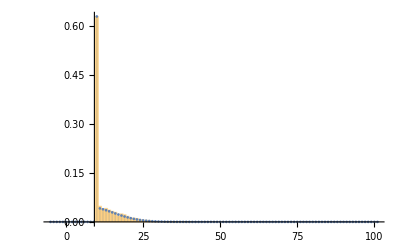

```mathematica
𝒟3=Piecewise[{{0,x<10},{1/2 Erfc[(-10+μ)/(√2 σ)],x==10}},1/2 (-Erf[(Floor[x]-μ)/(√2 σ)]+Erf[(1+Ceiling[x]-μ)/(√2 σ)])]
loss=Total@Abs@Table[𝒟3-Count[demons[[All,3]],x]/demonsNum,{x,0,100}];
solution=NMinimize[{loss,σ>1},{μ,σ}]
Show[Histogram[demons[[All,3]],{1},"Probability"],DiscretePlot[𝒟3/.solution[[2]],{x,-5,101},PlotStyle->Thick],PlotRange->All]
```

```mathematica
Round@RandomVariate[CensoredDistribution[{10,40},NormalDistribution[7.5,8.5]],100000];
KolmogorovSmirnovTest[%,demons[[All,3]],{"PValue","ShortTestConclusion"}]
```

{0.814251,Do not reject}

Piecewise[{{0, x<10}, {1/2 Erfc[(-10+μ)/(√2 σ)], x==10}, {0, x>100}, {1/2 (1+Erf[(-100+μ)/(√2 σ)]), x==100}, {1/2 (Erf[(1-μ+Ceiling[x])/(√2 σ)]-Erf[(-μ+Floor[x])/(√2 σ)]), True}}]

{0.122681,{μ→49.5134,σ→20.5069}}

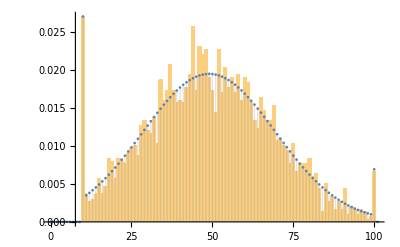

```mathematica
𝒟2=Piecewise[{{0,x<10},{1/2 Erfc[(-10+μ)/(√2 σ)],x==10},{0,x>100},{1/2 (1+Erf[(-100+μ)/(√2 σ)]),x==100}},1/2 (-Erf[(Floor[x]-μ)/(√2 σ)]+Erf[(1+Ceiling[x]-μ)/(√2 σ)])]
loss=Total@Abs@Table[𝒟2-Count[demons[[All,2]],x]/demonsNum,{x,0,100}];
solution=NMinimize[{loss,0<μ<100,σ>1},{μ,σ}]
Show[Histogram[demons[[All,2]],{1},"Probability"],DiscretePlot[𝒟2/.solution[[2]],{x,0,101},PlotStyle->Thick],PlotRange->All]
```

```mathematica
Floor@RandomVariate[CensoredDistribution[{10,100},NormalDistribution[50,20]],100000];
KolmogorovSmirnovTest[%,demons[[All,2]],{"PValue","ShortTestConclusion"}]
```

{0.443446,Do not reject}